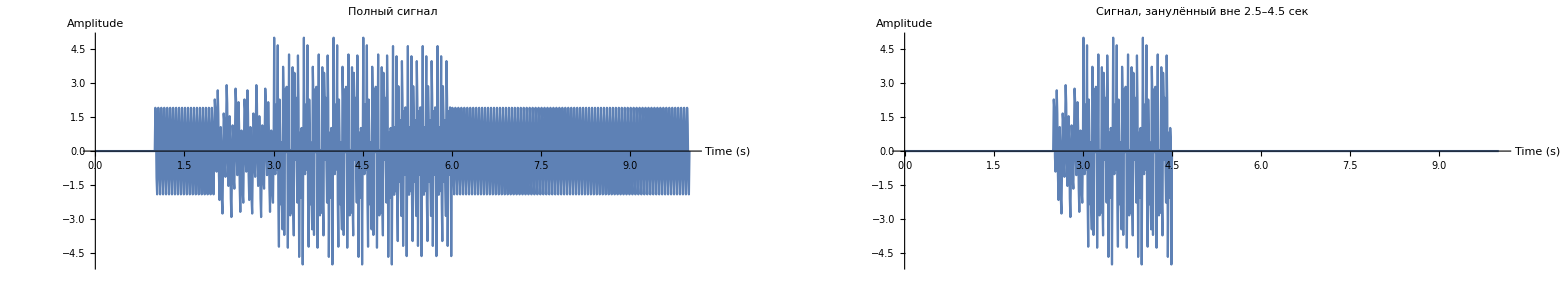

```mathematica
spec=<|MaxTime->10,SampleRate->100,Components->{<|Amplitude->2,Frequency->20,TStart->1,TEnd->10|>,<|Amplitude->3,Frequency->32,TStart->3,TEnd->6|>,<|Amplitude->1,Frequency->6,TStart->2,TEnd->5|>}|>;


data=Table[{t,Total@Map[If[#[TStart]<=t<=#[TEnd],1,0]*#[Amplitude]*Sin[2 Pi t #[Frequency]]&,spec[Components]]},{t,0,spec[MaxTime],1/spec[SampleRate]}];


cut=<|Start->2.5,End->4.5|>;


maskedData=Map[{#[[1]],If[cut[Start]<=#[[1]]<=cut[End],#[[2]],0]}&,data];


p1=ListLinePlot[data,PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Полный сигнал",ImageSize->1000,AspectRatio->1/5];

p2=ListLinePlot[maskedData,PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Сигнал, занулённый вне 2.5–4.5 сек",ImageSize->1000,AspectRatio->1/5];

GraphicsRow[{p1,p2}]
```